### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
FromReducedRankRuleSet[{"AB"-> "BBA", "B" -> "AA"}]
```

<|Index→50471770,QCode→34243432423,RuleSet→{AB→BBA,B→AA}|>

```mathematica
rsoc1 = FromReducedRankRuleSet[{"AB"-> "BBA", "B" -> "AA"}]
```

<|Index→50471770,QCode→34243432423,RuleSet→{AB→BBA,B→AA}|>

We can pull out the ruleset itself:

```mathematica
rsoc1[["RuleSet"]]
```

{AB→BBA,B→AA}

We generate the sessie and its causal network, again giving it a convenient name:


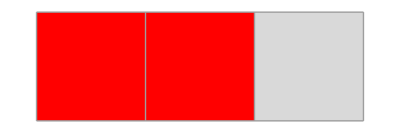

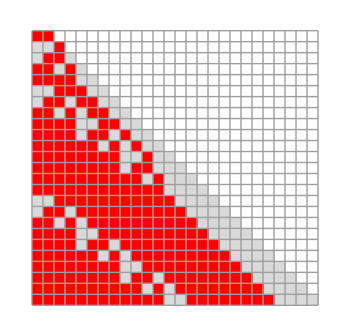
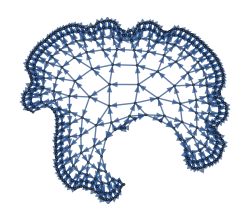
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssoc1=SSS[rsoc1[["RuleSet"]], "BB",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->25,NetMax->400,NetSize->250,SSSSize->350,HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sssoc1[["Net"]]//Sort//Short
```

{1→2,1→3,2→3,2→4,3→4,3→5,3→6,4→9,4→12,«775»,393→396,394→395,395→397,396→397,396→398,396→399,397→398,398→400,399→400}

```mathematica
ndsoc1=ToNetDifferenceSets[sssoc1[["Net"]]]
```

{{1,2},{1,2},{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2},{1},{},{1,2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1,2,3},{1},{2},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[ndsoc1,{1}]
```

{{108},{111},{114},{117},{120},{123},{126},{129},{132},{135},{138},{141},{144},{147},{150},{153},{156},{159},{162},{165},{168},{171},{174},{177},{181},{184},{187},{190},{193},{196},{199},{202},{205},{208},{211},{214},{217},{220},{223},{226},{229},{232},{235},{238},{241},{244},{247},{250},{253},{256},{259},{262},{265},{268},{271},{274},{277},{280},{283},{286},{289},{292},{295},{298},{301},{304},{307},{310},{313},{316},{319},{322},{325},{328},{331},{334},{337},{340},{343},{346},{349},{352},{355},{358},{361},{364},{367},{370},{373},{376},{379},{382},{385},{388},{391},{394},{397},{399}}

```mathematica
ndsoc1[[1;;107]]
```

{{1,2},{1,2},{1,2,3},{5,8},{1,2},{1,2,3},{1,8,9},{2,11,14},{1,2,3},{1,15,18},{2,20,23},{1,2},{1,24,27},{29,32},{1,2},{1,2,3},{1,32,33},{2,35,38},{1,2,3},{1,39,42},{2,44,47},{1,2,3},{1,48,51},{2,53,56},{1,2,3},{1,57,60},{2,62,65},{1,2,3},{1,66,69},{2,71,74},{1,2,3},{1,75,78},{2,80,83},{1,2,3},{1,84,87},{2,89,92},{1,2,3},{1,93,96},{2,98,101},{1,2,3},{1,102,105},{2,107,110},{1,2,3},{1,111,114},{2,116,119},{1,2},{1,120,123},{125,128},{1,2},{1,2,3},{1,128,129},{2,131,134},{1,2,3},{1,135,138},{2,140,143},{1,2,3},{1,144,147},{2,149,152},{1,2,3},{1,153,156},{2,158,161},{1,2,3},{1,162,165},{2,167,170},{1,2,3},{1,171,174},{2,176,179},{1,2,3},{1,180,183},{2,185,188},{1,2,3},{1,189,192},{2,194,197},{1,2,3},{1,198,201},{2,203,206},{1,2,3},{1,207,210},{2,212,215},{1,2,3},{1,216,219},{2,221,224},{1,2,3},{1,225,228},{2,230,233},{1,2,3},{1,234,237},{2,239,242},{1,2,3},{1,243,246},{2,248,251},{1,2,3},{1,252,255},{2,257,260},{1,2,3},{1,261,264},{2,266,269},{1,2,3},{1,270,273},{2,275,278},{1,2,3},{1,279,282},{2,284,287},{1,2,3},{1,288,291},{2,293},{1,2,3}}

Try the reduction:

```mathematica
rsloc1=ReduceSetList[ndsoc1[[1;;107]]]
```

DifferenceRoot::ieqn: The supplied equation in Function[{y,n},{0+(0+Times[«2»]+Times[«2»]) y[n]+(0+Times[«2»]+Times[«2»]) y[Plus[«2»]]+(0+Times[«2»]) y[Plus[«2»]]==0,y[1]==0,y[0]==29/2394}] is not a linear difference equation with polynomial coefficients.

{€^2[{1,2}],{1,2,3},{5,8},{1,2},€_(n$2⊨1)^2[€_(n$1⊨1)^2[{1,2+(-1+n$1) (6+7 (-1+n$2)),3+(-1+n$1) (6+9 (-1+n$2))}],{2,11+9 (-1+n$2),14+9 (-1+n$2)}],{1,2},{1,24,27},{29,32},{1,2},€_(n$1⊨1)^2[{1,2+30 (-1+n$1),3+30 (-1+n$1)}],{2,35,38},€_(n$1⊨1)^2[{1,2+37 (-1+n$1),3+39 (-1+n$1)}],{2,44,47},€_(n$1⊨1)^2[{1,2+46 (-1+n$1),3+48 (-1+n$1)}],{2,53,56},€_(n$1⊨1)^2[{1,2+55 (-1+n$1),3+57 (-1+n$1)}],{2,62,65},€_(n$1⊨1)^2[{1,2+64 (-1+n$1),3+66 (-1+n$1)}],{2,71,74},€_(n$1⊨1)^2[{1,2+73 (-1+n$1),3+75 (-1+n$1)}],{2,80,83},€_(n$1⊨1)^2[{1,2+82 (-1+n$1),3+84 (-1+n$1)}],{2,89,92},€_(n$1⊨1)^2[{1,2+91 (-1+n$1),3+93 (-1+n$1)}],{2,98,101},€_(n$1⊨1)^2[{1,2+100 (-1+n$1),3+102 (-1+n$1)}],{2,107,110},€_(n$1⊨1)^2[{1,2+109 (-1+n$1),3+111 (-1+n$1)}],{2,116,119},{1,2},{1,120,123},{125,128},{1,2},€_(n$2⊨1)^18[€_(n$1⊨1)^2[{1,2+126 (-1+n$1) ∏_(K[1]=1)^(-1+n$2) (19/18+[K[1]]),3+9 (-1+n$1) (13+n$2)}],{2,122+9 n$2,125+9 n$2}],€_(n$1⊨1)^2[{1,2+286 (-1+n$1),3+288 (-1+n$1)}],{2,293},{1,2,3}}

The most compressed part is

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```